```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

290

289

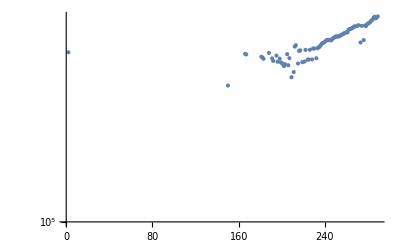

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{1*^5,All},
Joined->False
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|L1PhaseSet→-29.7465,L2PhaseSet→-47.4794,S1EL_xOffset→-0.0000420181,S1EL_yOffset→-0.0000628748,S2EL_xOffset→0.0000183352,S2EL_yOffset→-0.000258083,S2ER_xOffset→-0.0000404673,S2ER_yOffset→-0.000854228,S1ER_xOffset→-0.000603355,S1ER_yOffset→-0.000431498,Q5FFkG→-72.0898,Q4FFkG→-79.963,Q3FFkG→99.3855,Q2FFkG→126.348,Q1FFkG→-235.274,Q0FFkG→126.279,XC1FFkG→0.245582,XC3FFkG→-0.12992,YC1FFkG→-0.0000222919,YC2FFkG→-0.000224765,PDrive_mean_x→3.8237×10^-6,PDrive_mean_y→4.468×10^-7,PDrive_sigma_x→0.0000505714,PDrive_sigma_y→0.0000194436,PDrive_mean_xp→0.000497788,PDrive_mean_yp→-0.0000289063,PDrive_sigmaSI90_x→0.0000480765,PDrive_sigmaSI90_y→0.0000187924,PDrive_emitSI90_x→0.0000478954,PDrive_emitSI90_y→8.7401×10^-6,PDrive_zLen→0.0000380968,PDrive_zCentroid→991.332,PWitness_mean_x→-9.63×10^-8,PWitness_mean_y→-4.0319×10^-6,PWitness_sigma_x→0.0000460398,PWitness_sigma_y→0.0000222041,PWitness_mean_xp→0.000381232,PWitness_mean_yp→-0.0000558731,PWitness_sigmaSI90_x→0.0000391264,PWitness_sigmaSI90_y→0.0000185039,PWitness_emitSI90_x→0.0000278812,PWitness_emitSI90_y→4.9497×10^-6,PWitness_zLen→0.0000684848,PWitness_zCentroid→991.332,bunchSpacing→0.000148552,transverseCentroidOffset→5.9519×10^-6,lostChargeFraction→0.,maximizeMe→175221.|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L1PhaseSet : -29.7465390751
L2PhaseSet : -47.4793569981
S1EL_xOffset : -0.0000420181
S1EL_yOffset : -0.0000628748
S2EL_xOffset : 0.0000183352
S2EL_yOffset : -0.0002580827
S2ER_xOffset : -0.0000404673
S2ER_yOffset : -0.0008542281
S1ER_xOffset : -0.000603355
S1ER_yOffset : -0.0004314976
Q5FFkG : -72.0898330248
Q4FFkG : -79.9629544852
Q3FFkG : 99.385548071
Q2FFkG : 126.3483884741
Q1FFkG : -235.2744078772
Q0FFkG : 126.2792932619
XC1FFkG : 0.2455823504
XC3FFkG : -0.1299197779
YC1FFkG : -0.0000222919
YC2FFkG : -0.0002247647
PDrive_mean_x : 3.8237e-6
PDrive_mean_y : 4.468e-7
PDrive_sigma_x : 0.0000505714
PDrive_sigma_y : 0.0000194436
PDrive_mean_xp : 0.0004977878
PDrive_mean_yp : -0.0000289063
PDrive_sigmaSI90_x : 0.0000480765
PDrive_sigmaSI90_y : 0.0000187924
PDrive_emitSI90_x : 0.0000478954
PDrive_emitSI90_y : 8.7401e-6
PDrive_zLen : 0.0000380968
PDrive_zCentroid : 991.3316271964
PWitness_mean_x : -9.63e-8
PWitness_mean_y : -4.0319e-6
PWitness_sigma_x : 0.0000460398
PWitness_sigma_y : 0.0000222041
PWitness_mean_xp : 0.0003812318
PWitness_mean_yp : -0.0000558731
PWitness_sigmaSI90_x : 0.0000391264
PWitness_sigmaSI90_y : 0.0000185039
PWitness_emitSI90_x : 0.0000278812
PWitness_emitSI90_y : 4.9497e-6
PWitness_zLen : 0.0000684848
PWitness_zCentroid : 991.3317757487
bunchSpacing : 0.0001485523
transverseCentroidOffset : 5.9519e-6
lostChargeFraction : 0.
maximizeMe : 175221.3821817099

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

5.9519×10^-6

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L1PhaseSet","L2PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L1PhaseSet,L2PhaseSet,Q0FFkG,Q1FFkG,Q2FFkG,Q3FFkG,Q4FFkG,Q5FFkG,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_zLen"
```

PDrive_zLen

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

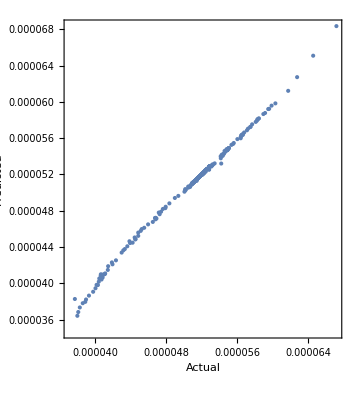

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
Minimize[
lm["BestFit"],
Symbol[#]&/@freeVarsMathematica
]
```

NMinimize::ubnd: The problem is unbounded.

{-∞,{L1PhaseSet→Indeterminate,L2PhaseSet→Indeterminate,Q0FFkG→Indeterminate,Q1FFkG→Indeterminate,Q2FFkG→Indeterminate,Q3FFkG→Indeterminate,Q4FFkG→Indeterminate,Q5FFkG→Indeterminate,S1ELxOffset→Indeterminate,S1ELyOffset→Indeterminate,S1ERxOffset→Indeterminate,S1ERyOffset→Indeterminate,S2ELxOffset→Indeterminate,S2ELyOffset→Indeterminate,S2ERxOffset→Indeterminate,S2ERyOffset→Indeterminate,XC1FFkG→Indeterminate,XC3FFkG→Indeterminate,YC1FFkG→Indeterminate,YC2FFkG→Indeterminate}}

*facepalm* It’s a linear model, obviously it’s unbounded

```mathematica
lm["ANOVATable"]
```

General::munfl: Exp[-755.757] is too small to represent as a normalized machine number; precision may be lost.

| DF | SS | MS | F-Statistic | P-Value
L1PhaseSet | 1 | 1.563×10^-10 | 1.563×10^-10 | 1810.69 | 3.18732×10^-121
L2PhaseSet | 1 | 6.34294×10^-9 | 6.34294×10^-9 | 73481.3 | 0.
Q0FFkG | 1 | 8.75566×10^-15 | 8.75566×10^-15 | 0.101432 | 0.750366
Q1FFkG | 1 | 3.41469×10^-14 | 3.41469×10^-14 | 0.395583 | 0.529915
Q2FFkG | 1 | 2.63501×10^-14 | 2.63501×10^-14 | 0.305259 | 0.581064
Q3FFkG | 1 | 5.89823×10^-14 | 5.89823×10^-14 | 0.683294 | 0.40919
Q4FFkG | 1 | 4.26202×10^-14 | 4.26202×10^-14 | 0.493744 | 0.482872
Q5FFkG | 1 | 4.90687×10^-14 | 4.90687×10^-14 | 0.568448 | 0.451538
S1ELxOffset | 1 | 3.19605×10^-15 | 3.19605×10^-15 | 0.0370254 | 0.847559
S1ELyOffset | 1 | 4.01674×10^-14 | 4.01674×10^-14 | 0.465329 | 0.495733
S1ERxOffset | 1 | 8.69771×10^-14 | 8.69771×10^-14 | 1.00761 | 0.316382
S1ERyOffset | 1 | 5.74877×10^-17 | 5.74877×10^-17 | 0.00066598 | 0.979431
S2ELxOffset | 1 | 4.95203×10^-14 | 4.95203×10^-14 | 0.57368 | 0.449466
S2ELyOffset | 1 | 2.54496×10^-13 | 2.54496×10^-13 | 2.94827 | 0.087125
S2ERxOffset | 1 | 4.7035×10^-13 | 4.7035×10^-13 | 5.44888 | 0.02032
S2ERyOffset | 1 | 3.15188×10^-14 | 3.15188×10^-14 | 0.365137 | 0.546178
XC1FFkG | 1 | 2.4948×10^-15 | 2.4948×10^-15 | 0.0289016 | 0.865135
XC3FFkG | 1 | 8.44501×10^-15 | 8.44501×10^-15 | 0.0978332 | 0.754689
YC1FFkG | 1 | 1.02917×10^-15 | 1.02917×10^-15 | 0.0119226 | 0.913133
YC2FFkG | 1 | 4.93701×10^-15 | 4.93701×10^-15 | 0.057194 | 0.81117
Error | 268 | 2.31339×10^-11 | 8.63205×10^-14 |  | 
Total | 288 | 6.52354×10^-9 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Plot::plld: Endpoints for x in {x,0.,0.} must have distinct machine-precision numerical values.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[x,{x,Min[lm[Response]],Max[lm[Response]]},PlotStyle→Red]].

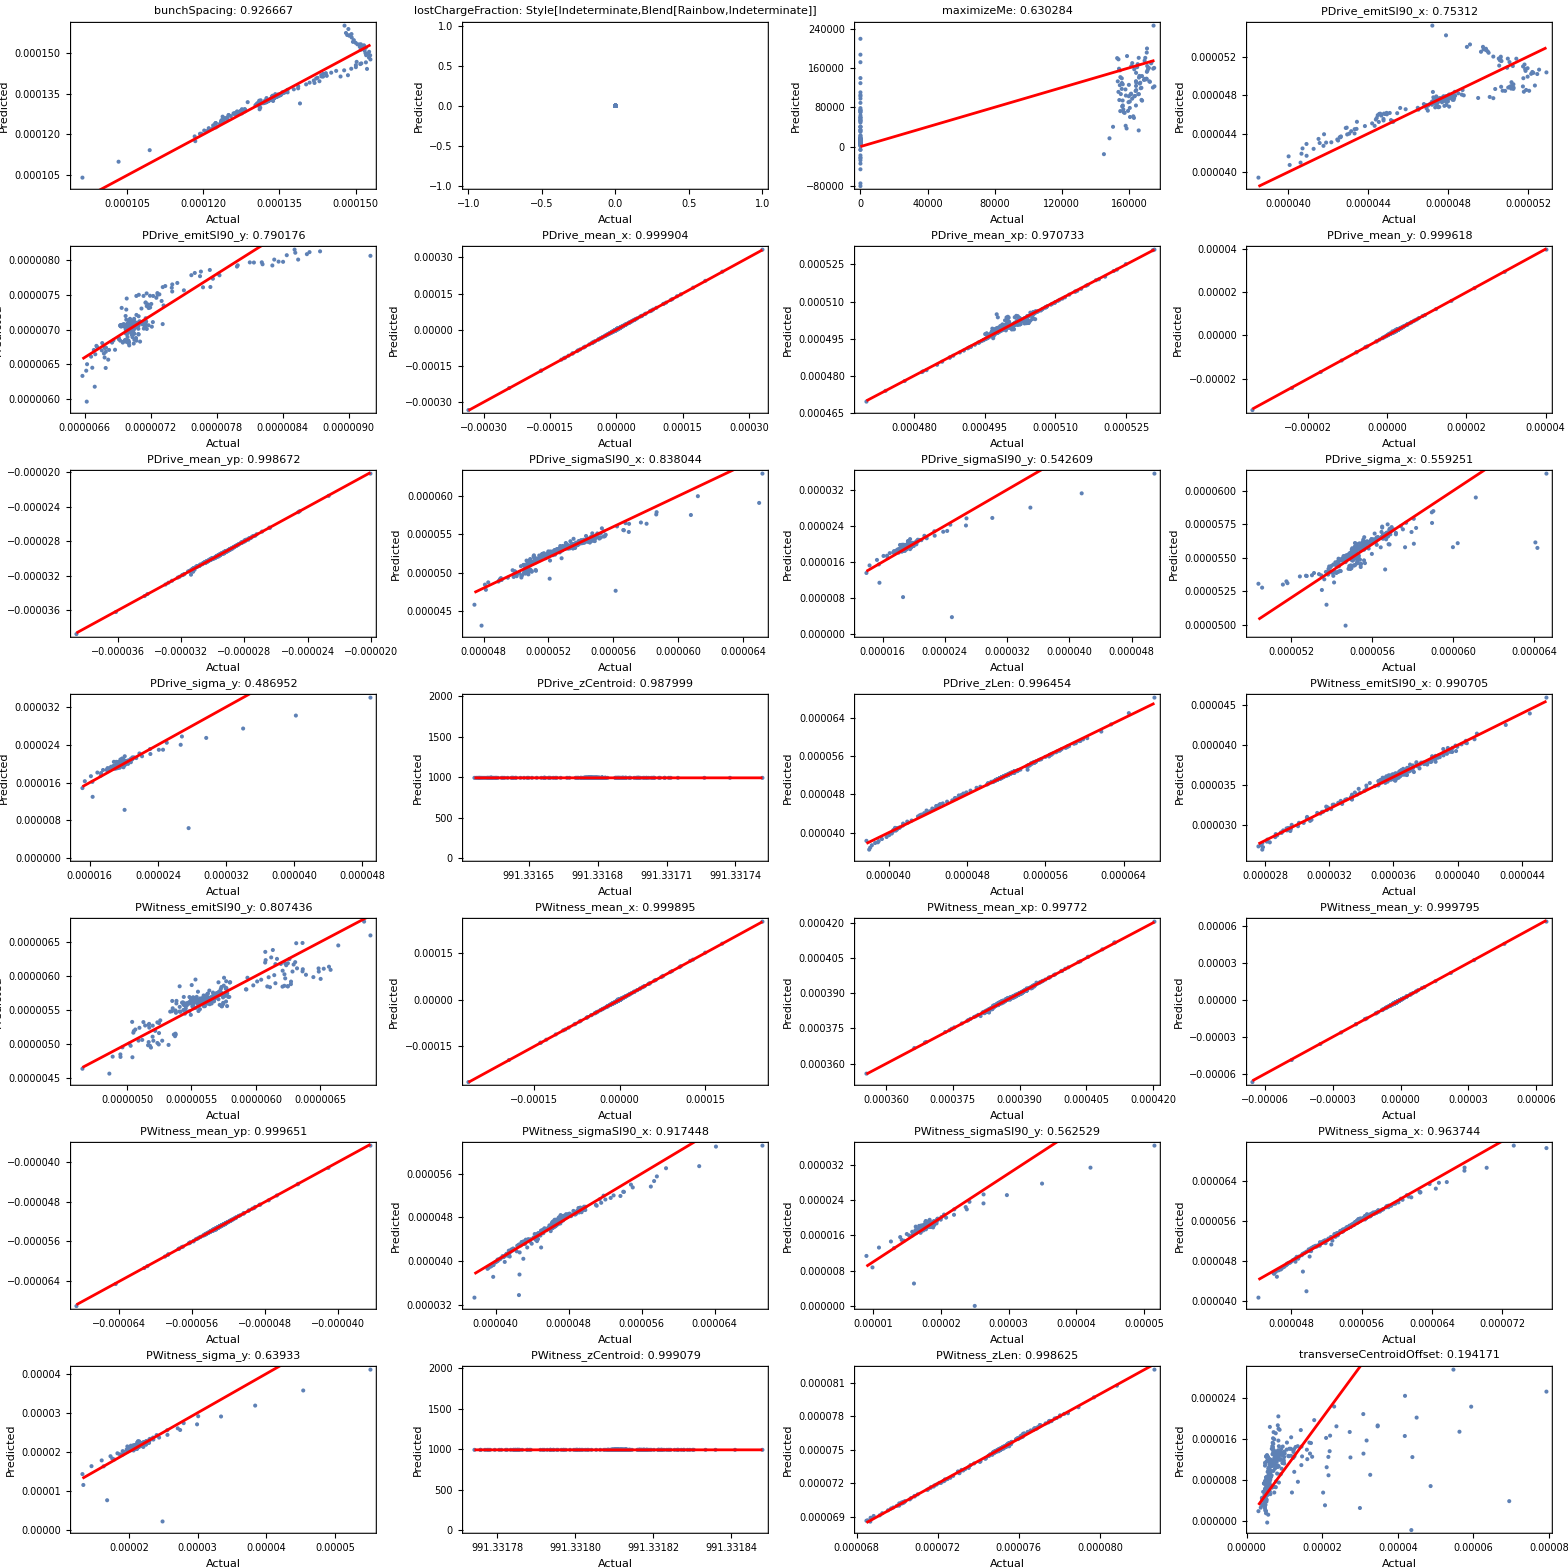

```mathematica
displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```